```mathematica
Get["http://www.fmt.if.usp.br/~gtlandi/download/melt.m"]
```

```mathematica
XXXUMarkovianfunction[γ_,T_,Δt_]:= Module[{Ν,gDown,gUp,H0Markovian,HIdownMarkovian,ω,HIupMarkovian,USATotalMarkovian},
ω=1;
Ν=1/(Exp[ω/T]-1);
gDown=Sqrt[γ (Ν+1)];
gUp=Sqrt[γ (Ν)];
H0Markovian=KronEye[σz/2,3,1]+KronEye[σz/2,3,2]+KronEye[σz/2,3,3];
HIdownMarkovian = -(1/2)(1/Sqrt[Δt])gDown (KronEye[σx,3,1].KronEye[σx,3,2]+KronEye[σy,3,1].KronEye[σy,3,2]+KronEye[σz,3,1].KronEye[σz,3,2]);
HIupMarkovian = -(1/2)(1/Sqrt[Δt])gUp (KronEye[σx,3,1].KronEye[σx,3,3]+KronEye[σy,3,1].KronEye[σy,3,3]+KronEye[σz,3,1].KronEye[σz,3,3]);
USATotalMarkovian = MatrixExp[-ⅈ (H0Markovian+HIdownMarkovian+HIupMarkovian)Δt]
]
XXXMarkovianSteadyStateCurrent[ρA_,γ_,T_,Δt_]:=Module[{SystemSS,JointAncillaStateAfter,Ancilla1ReducedState,Ancilla2ReducedState,CurrentA1,CurrentA2},
SystemSS = CollisionModelSteadyState[XXXUMarkovianfunction[γ,T,Δt],ρA];
JointAncillaStateAfter = CollisionMap[SystemSS,XXXUMarkovianfunction[γ,T,Δt],ρA,1,"all"][[All,2]][[2]];
Ancilla1ReducedState = PTr[JointAncillaStateAfter,{2}];
Ancilla2ReducedState =PTr[JointAncillaStateAfter,{1}];
CurrentA1 = Tr[(σz/2).(Ancilla1ReducedState-PTr[ρA,{2}])]//Chop;
CurrentA2 = Tr[(σz/2).(Ancilla2ReducedState-PTr[ρA,{1}])]//Chop;
{CurrentA1,CurrentA2}];

XXUMarkovianfunction[γ_,T_,Δt_]:= Module[{Ν,gDown,gUp,H0Markovian,HIdownMarkovian,ω,HIupMarkovian,USATotalMarkovian},
ω=1;
Ν=1/(Exp[ω/T]-1);
gDown=Sqrt[γ (Ν+1)];
gUp=Sqrt[γ (Ν)];
H0Markovian=KronEye[σz/2,3,1]+KronEye[σz/2,3,2]+KronEye[σz/2,3,3];
HIdownMarkovian = -(1/2)(1/Sqrt[Δt])gDown (KronEye[σx,3,1].KronEye[σx,3,2]+KronEye[σy,3,1].KronEye[σy,3,2](*+KronEye[σz,3,1].KronEye[σz,3,2]*));
HIupMarkovian = -(1/2)(1/Sqrt[Δt])gUp (KronEye[σx,3,1].KronEye[σx,3,3]+KronEye[σy,3,1].KronEye[σy,3,3](*+KronEye[σz,3,1].KronEye[σz,3,3]*));
USATotalMarkovian = MatrixExp[-ⅈ (H0Markovian+HIdownMarkovian+HIupMarkovian)Δt]
]
XXMarkovianSteadyStateCurrent[ρA_,γ_,T_,Δt_]:=Module[{SystemSS,JointAncillaStateAfter,Ancilla1ReducedState,Ancilla2ReducedState,CurrentA1,CurrentA2},
SystemSS = CollisionModelSteadyState[XXUMarkovianfunction[γ,T,Δt],ρA];
JointAncillaStateAfter = CollisionMap[SystemSS,XXUMarkovianfunction[γ,T,Δt],ρA,1,"all"][[All,2]][[2]];
Ancilla1ReducedState = PTr[JointAncillaStateAfter,{2}];
Ancilla2ReducedState =PTr[JointAncillaStateAfter,{1}];
CurrentA1 = Tr[(σz/2).(Ancilla1ReducedState-PTr[ρA,{2}])]//Chop;
CurrentA2 = Tr[(σz/2).(Ancilla2ReducedState-PTr[ρA,{1}])]//Chop;
{CurrentA1,CurrentA2}]
```

```mathematica
γXXX=1;
γXX=1;
ρA1=out[Basis[2,2],Basis[2,2]];
ρA2=out[Basis[2,1],Basis[2,1]];
ρA= kron[ρA1,ρA2];
timesteps= Table[10^α,{α,-3,0,0.05}];
```

```mathematica
XXXCurrentsA1Low=Transpose[{timesteps,Table[XXXMarkovianSteadyStateCurrent[ρA,γXXX,0.5,Δts]/Δts,{Δts,timesteps}][[All,1]]}];
XXXCurrentsA1High=Transpose[{timesteps,Table[XXXMarkovianSteadyStateCurrent[ρA,γXXX,2,Δts]/Δts,{Δts,timesteps}][[All,1]]}];
```

```mathematica
XXCurrentsA1Low=Transpose[{timesteps,ParallelTable[XXMarkovianSteadyStateCurrent[ρA,γXX,0.5,Δts]/Δts,{Δts,timesteps}][[All,1]]}];
XXCurrentsA1High=Transpose[{timesteps,ParallelTable[XXMarkovianSteadyStateCurrent[ρA,γXX,2,Δts]/Δts,{Δts,timesteps}][[All,1]]}];
```

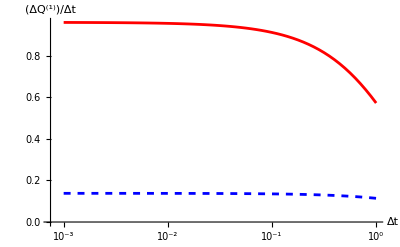

```mathematica
XXXCurrentPlot=ListLinePlot[{XXXCurrentsA1Low,XXXCurrentsA1High},AxesLabel->{"Δt","ΔQ^(1)/Δt"},AxesStyle->Directive[Black],ScalingFunctions->{"Log10",None},PlotStyle->{Directive[Blue,Dashed],Directive[Red]}]
```

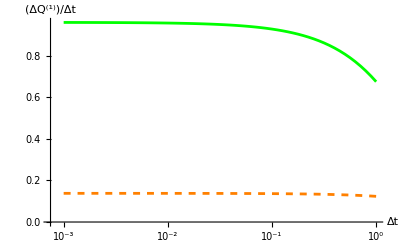

```mathematica
XXCurrentPlot=ListLinePlot[{XXCurrentsA1Low,XXCurrentsA1High},AxesLabel->{"Δt","ΔQ^(1)/Δt"},AxesStyle->Directive[Black],ScalingFunctions->{"Log10",None},PlotStyle->{Directive[Orange,Dashed],Directive[Green]}]
```

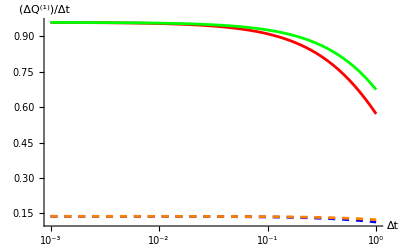

```mathematica
Show[XXXCurrentPlot,XXCurrentPlot,PlotRange->All]
```

```mathematica
XXXMarkovianSSTemp[ρA_,γ_,T_,Δt_]:=Module[{ω,U,ρA1,ρA2,ρSS,EffTemp,Δβ},
ω=1.;
U=XXXUMarkovianfunction[γ,T,Δt];
ρSS=CollisionModelSteadyState[U,ρA];
EffTemp = Quiet@NSolve[ρSS[[2,2]]==(1+(1/(2(1/(Exp[β ω]-1))+1)))/2,β][[1,1,2]];
Δβ= EffTemp-(1/T)//Chop
];
XXMarkovianSSTemp[ρA_,γ_,T_,Δt_]:=Module[{ω,U,ρA1,ρA2,ρSS,EffTemp,Δβ},
ω=1.;
U=XXUMarkovianfunction[γ,T,Δt];
ρSS=CollisionModelSteadyState[U,ρA];
EffTemp = Quiet@NSolve[ρSS[[2,2]]==(1+(1/(2(1/(Exp[β ω]-1))+1)))/2,β][[1,1,2]];
Δβ= EffTemp-(1/T)//Chop
];
```

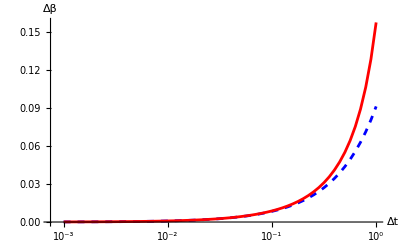

```mathematica
XXXSSTempsLow=ParallelTable[{Δts,XXXMarkovianSSTemp[ρA,γXXX,0.5,Δts]},{Δts,timesteps}];
XXXSSTempsHigh=ParallelTable[{Δts,XXXMarkovianSSTemp[ρA,γXX,2,Δts]},{Δts,timesteps}];

ListLinePlot[{XXXSSTempsLow,XXXSSTempsHigh},AxesStyle->Directive[Black],ScalingFunctions->{"Log10",None},PlotStyle->{Directive[Blue,Dashed],Directive[Red]},PlotRange->All,AxesLabel->{"Δt","Δβ"}]
```

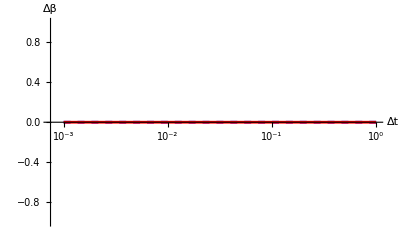

```mathematica
XXSSTempsLow=ParallelTable[{Δts,XXMarkovianSSTemp[ρA,γXX,0.5,Δts]},{Δts,timesteps}];
XXSSTempsHigh=ParallelTable[{Δts,XXMarkovianSSTemp[ρA,γXX,2,Δts]},{Δts,timesteps}];

ListLinePlot[{XXSSTempsLow,XXSSTempsHigh},AxesStyle->Directive[Black],ScalingFunctions->{"Log10",None},PlotStyle->{Directive[Blue,Dashed],Directive[Red]},PlotRange->All,AxesLabel->{"Δt","Δβ"}]
```

```mathematica
(*Export["XXXCurrents05.mx",XXXCurrentsA1Low]
Export["XXXCurrents2.mx",XXXCurrentsA1High]*)
```

```mathematica
(*Export["XXCurrents05.mx",XXCurrentsA1Low]
Export["XXCurrents2.mx",XXCurrentsA1High]*)
```

```mathematica
(*Export["XXXSSTemps05.mx",XXXSSTempsLow]
Export["XXXSSTemps2.mx",XXXSSTempsHigh]*)
```

```mathematica
(*Export["XXSSTemps05.mx",XXSSTempsLow]
Export["XXSSTemps2.mx",XXSSTempsHigh]*)
```